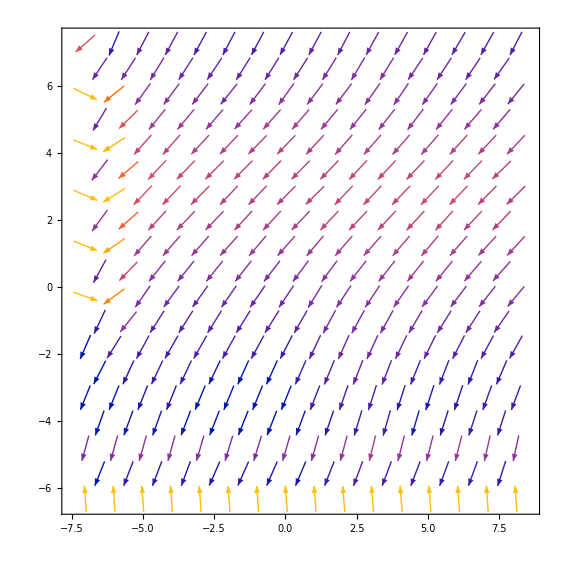

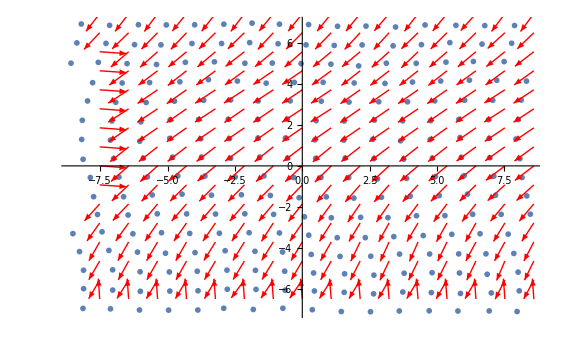

```mathematica
config = Import["/Users/pankaj/Documents/library/my-papers/in-progress/saswati-trial/MD_square_stable_hchi/results/time/new_cordinates_9990.dat","Table"][[All,2;;3]];
reference = Import["/Users/pankaj/Documents/library/my-papers/in-progress/saswati-trial/MD_square_stable_hchi/results/cordinates.dat","Table"][[All,2;;3]];
ListVectorPlot[Thread[{reference,config-reference}]]
Show[ListPlot[config],Graphics[  {Red,Arrowheads[0.01],Map[Arrow,Thread[{reference,reference+((config-reference)/Map[Norm,config-reference,1])}]] }  ,Axes->True,AspectRatio->0.5,ImageSize->800,PlotRange->{{-9,9},{-9,9}}]]
```

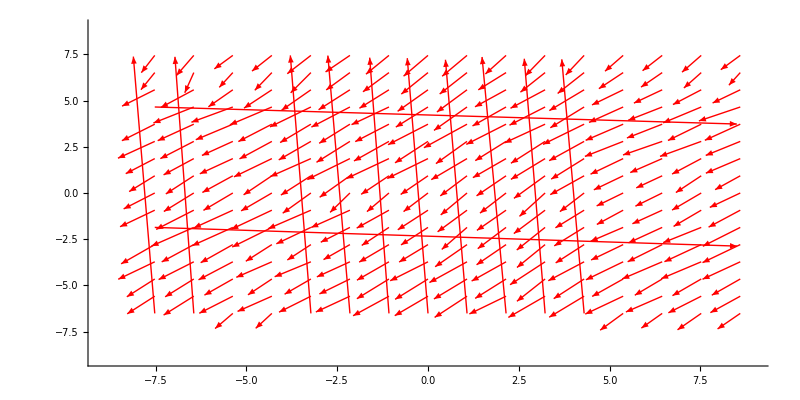

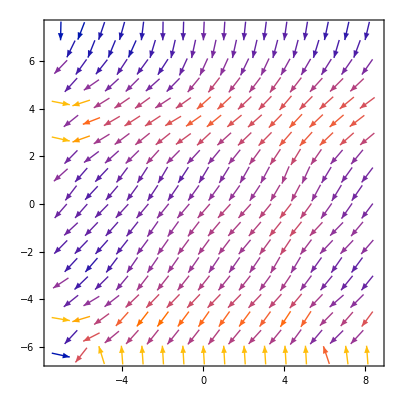

```mathematica
Graphics[  {Red,Arrowheads[0.01],Map[Arrow,Thread[{reference,reference+((config-reference))}]] }  ,Axes->True,AspectRatio->0.5,ImageSize->800,PlotRange->{{-9,9},{-9,9}}]
```

ListVectorPlot::vfldata: {{{0,0},{1,1}},{{0,0},{1,-1}}} is not a valid vector field dataset or a valid list of datasets.

ListVectorPlot[{{{0,0},{1,1}},{{0,0},{1,-1}}}]

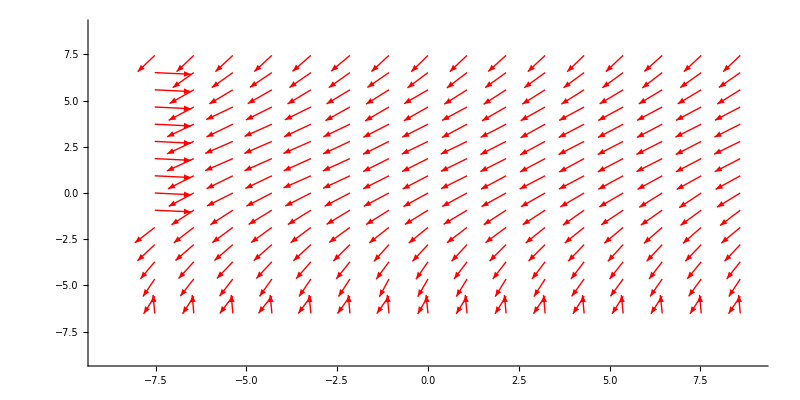

```mathematica
ListVectorPlot[{{{0,0},{1,1}},{{0,0},{1,-1}}}]
```

```mathematica
ListVectorPlot[{{{0,0},{1,1}},{{0,0},{1,-1}}}]
```

ListVectorPlot::vfldata: {{{0,0},{1,1}},{{0,0},{1,-1}}} is not a valid vector field dataset or a valid list of datasets.

ListVectorPlot[{{{0,0},{1,1}},{{0,0},{1,-1}}}]

```mathematica
{{{0,0},{1,1}},{{0,0},{1,-1}}}//MatrixForm
```

((0
0) | (1
1)
(0
0) | (1
-1))

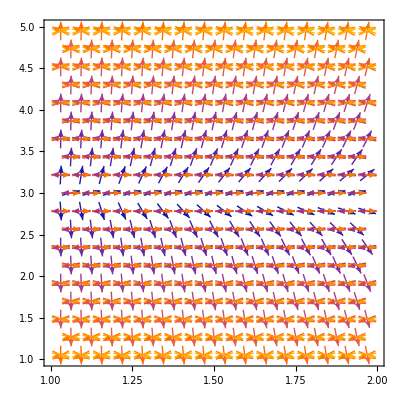

```mathematica
ListVectorPlot[Thread[{Table[{x,y},{x,-2,2,1},{y,-2,2,1}],Table[{0,0.1},{x,-2,2,1},{y,-2,2,1}]+0.1}]]
```

```mathematica
Thread[{Table[{x,y},{x,-2,2,1},{y,-2,2,1}],Table[{x,y},{x,-2,2,1},{y,-2,2,1}]}]
```

{{{{-2,-2},{-2,-1},{-2,0},{-2,1},{-2,2}},{{-2,-2},{-2,-1},{-2,0},{-2,1},{-2,2}}},{{{-1,-2},{-1,-1},{-1,0},{-1,1},{-1,2}},{{-1,-2},{-1,-1},{-1,0},{-1,1},{-1,2}}},{{{0,-2},{0,-1},{0,0},{0,1},{0,2}},{{0,-2},{0,-1},{0,0},{0,1},{0,2}}},{{{1,-2},{1,-1},{1,0},{1,1},{1,2}},{{1,-2},{1,-1},{1,0},{1,1},{1,2}}},{{{2,-2},{2,-1},{2,0},{2,1},{2,2}},{{2,-2},{2,-1},{2,0},{2,1},{2,2}}}}

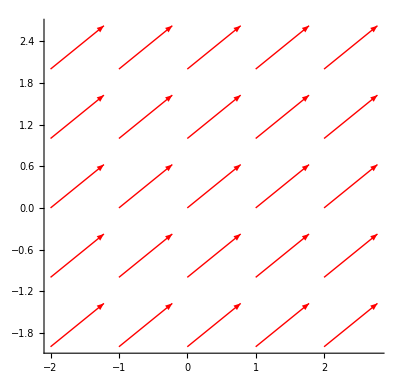

```mathematica
Graphics[{Red,Arrowheads[0.02],Map[Arrow,Thread[{Flatten[Table[{x,y},{x,-2,2,1},{y,-2,2,1}],1],Flatten[Table[{x,y}+{0.5,0.4}/Norm[{0.5,0.4}],{x,-2,2,1},{y,-2,2,1}],1]}]] }  ,Axes->True]
```

```mathematica
Graphics[Map[Arrow,Thread[{Flatten[Table[{x,y},{x,-2,2,1},{y,-2,2,1}],1],Flatten[Table[{x1+0.1,y1+0.1}/Norm[{x1+0.1,y1+0.1}],{x1,-2,2,1},{y1,-2,2,1}],1]}    ][[1]]   ]]
```

-Graphics-

```mathematica
Thread[{Flatten[Table[{x,y},{x,-2,2,1},{y,-2,2,1}],1],Flatten[Table[{x,y},{x,-2,2,1},{y,-2,2,1}],1]+0.1}]//MatrixForm
```

((-2
-2) | (-1.9
-1.9)
(-2
-1) | (-1.9
-0.9)
(-2
0) | (-1.9
0.1)
(-2
1) | (-1.9
1.1)
(-2
2) | (-1.9
2.1)
(-1
-2) | (-0.9
-1.9)
(-1
-1) | (-0.9
-0.9)
(-1
0) | (-0.9
0.1)
(-1
1) | (-0.9
1.1)
(-1
2) | (-0.9
2.1)
(0
-2) | (0.1
-1.9)
(0
-1) | (0.1
-0.9)
(0
0) | (0.1
0.1)
(0
1) | (0.1
1.1)
(0
2) | (0.1
2.1)
(1
-2) | (1.1
-1.9)
(1
-1) | (1.1
-0.9)
(1
0) | (1.1
0.1)
(1
1) | (1.1
1.1)
(1
2) | (1.1
2.1)
(2
-2) | (2.1
-1.9)
(2
-1) | (2.1
-0.9)
(2
0) | (2.1
0.1)
(2
1) | (2.1
1.1)
(2
2) | (2.1
2.1))

```mathematica
Map[Norm,config]
```

{10.6445,9.81628,9.1817,8.57294,8.04454,7.48069,7.10376,6.81245,6.82855,7.02206,7.27887,7.76588,8.29221,8.92713,9.66744,10.5252,10.7122,9.90079,9.13732,8.45468,7.8822,7.48545,7.26272,7.19977,7.16808,7.33363,7.6108,8.06316,8.63851,9.30463,10.0391,10.7748,10.1972,9.30195,8.47572,7.7003,7.08941,6.61454,6.39601,6.2244,6.2237,6.36749,6.76412,7.19477,7.83445,8.5914,9.31849,10.2,9.73196,8.81615,7.97782,7.16871,6.45226,5.86207,5.52601,5.31204,5.24027,5.43916,5.87756,6.38693,7.0837,7.90331,8.66409,9.57167,9.37918,8.44753,7.51841,6.63713,5.88744,5.18172,4.73224,4.45452,4.335,4.53225,4.94331,5.59809,6.35881,7.18593,8.04318,8.97353,9.12981,8.13284,7.16581,6.22221,5.38072,4.5991,4.00074,3.5988,3.3991,3.5302,4.06904,4.75845,5.58614,6.50906,7.4424,8.37036,8.90653,7.92361,6.90513,5.95671,5.01806,4.11505,3.40133,2.80863,2.46342,2.67263,3.18541,4.03401,4.87224,5.86277,6.8935,7.94539,8.45052,7.89972,6.91859,5.84084,4.81674,3.84377,2.90004,2.0829,1.60678,1.71158,2.40382,3.32893,4.31812,5.38163,6.48097,7.45908,8.24881,7.91299,6.77604,5.7602,4.78188,3.71572,2.63496,1.61984,0.714578,0.91636,1.78713,2.83841,3.94299,5.03112,6.06943,7.16903,8.10068,8.03674,6.97458,5.86967,4.77028,3.71598,2.62065,1.57606,0.604797,0.648688,1.69954,2.76871,3.81428,4.86013,5.97584,7.04624,8.15527,8.14045,7.10649,6.06257,4.98123,3.94639,2.90844,2.03147,1.38602,1.3668,2.03025,2.99826,3.96975,5.01093,6.02204,7.08076,8.43628,8.33127,7.25282,6.2836,5.28141,4.32733,3.40332,2.69407,2.21116,2.28865,2.69883,3.4559,4.37946,5.35853,6.34557,7.35647,8.76004,8.47685,7.5912,6.56322,5.68444,4.72375,3.9486,3.40972,3.1796,3.18069,3.53613,4.20664,4.94888,5.79435,6.75936,7.73518,9.29157,8.79695,7.79045,6.93998,6.07096,5.33172,4.66087,4.30423,4.00204,4.16772,4.4703,5.00879,5.77595,6.49116,7.40091,8.32261,9.95791,9.03768,8.16422,7.41104,6.65431,5.99568,5.47051,5.06448,4.93471,5.08734,5.43676,5.85604,6.58779,7.30893,8.14933,8.9399,10.2229,9.38162,8.61058,7.88432,7.29011,6.75809,6.23698,5.91166,5.90458,6.09283,6.34715,6.7819,7.42983,8.13531,8.91677,9.74234}

```mathematica
Table[1/Norm[{x+0.5,y+0.5}]{x+0.5,y+0.5},{x,-2,2,1},{y,-2,2,1}]
```

{{{-0.707107,-0.707107},{-0.948683,-0.316228},{-0.948683,0.316228},{-0.707107,0.707107},{-0.514496,0.857493}},{{-0.316228,-0.948683},{-0.707107,-0.707107},{-0.707107,0.707107},{-0.316228,0.948683},{-0.196116,0.980581}},{{0.316228,-0.948683},{0.707107,-0.707107},{0.707107,0.707107},{0.316228,0.948683},{0.196116,0.980581}},{{0.707107,-0.707107},{0.948683,-0.316228},{0.948683,0.316228},{0.707107,0.707107},{0.514496,0.857493}},{{0.857493,-0.514496},{0.980581,-0.196116},{0.980581,0.196116},{0.857493,0.514496},{0.707107,0.707107}}}

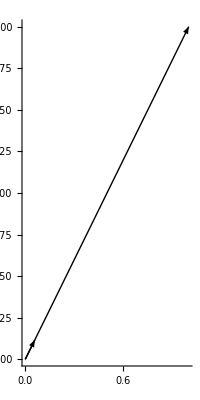

```mathematica
Show[Graphics[Arrow[1/Norm[{10,14}]{{0,0},{1,2}}],Axes->True],Graphics[Arrow[{{0,0},{1,2}}],Axes->True]]
```

```mathematica
Thread[{Flatten[Table[{x,y},{x,-2,2,1},{y,-2,2,1}],1],Flatten[Table[{x1+0.1,y1+0.1}/Norm[{x1+0.1,y1+0.1}],{x1,-2,2,1},{y1,-2,2,1}],1]}    ][[1]]
```

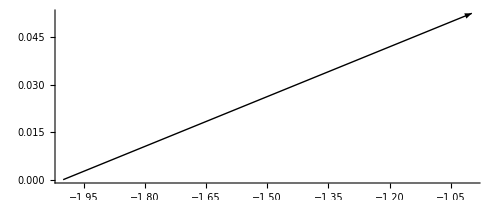

```mathematica
Graphics[Arrow[{Thread[{Flatten[Table[{x,y},{x,-2,2,1},{y,-2,2,1}],1],Flatten[Table[{x1+0.1,y1+0.1}/Norm[{x1+0.1,y1+0.1}],{x1,-2,2,1},{y1,-2,2,1}],1]}    ][[3]] }],Axes->True]
```

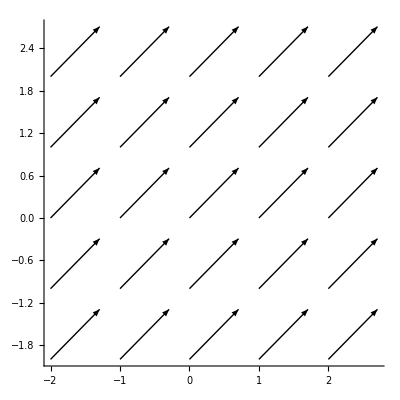

```mathematica
Graphics[Map[Arrow,Thread[{Flatten[Table[{x1,y1},{x1,-2,2,1},{y1,-2,2,1}],1],Flatten[Table[{x1,y1}+{0.3,0.3}/Norm[{0.3,0.3}],{x1,-2,2,1},{y1,-2,2,1}],1]}]],Axes->True]
```

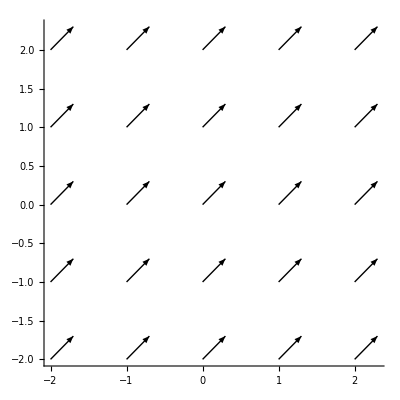

```mathematica
Graphics[Map[Arrow,Thread[{Flatten[Table[{x1,y1},{x1,-2,2,1},{y1,-2,2,1}],1],Flatten[Table[{x1+0.3,y1+0.3},{x1,-2,2,1},{y1,-2,2,1}],1]}]],Axes->True]
```

```mathematica
{1,1}/Norm[{0.3,0.3}]
```

{2.35702,2.35702}

```mathematica
Map[Norm,reference+config-reference,1]
```

{10.6445,9.81628,9.1817,8.57294,8.04454,7.48069,7.10376,6.81245,6.82855,7.02206,7.27887,7.76588,8.29221,8.92713,9.66744,10.5252,10.7122,9.90079,9.13732,8.45468,7.8822,7.48545,7.26272,7.19977,7.16808,7.33363,7.6108,8.06316,8.63851,9.30463,10.0391,10.7748,10.1972,9.30195,8.47572,7.7003,7.08941,6.61454,6.39601,6.2244,6.2237,6.36749,6.76412,7.19477,7.83445,8.5914,9.31849,10.2,9.73196,8.81615,7.97782,7.16871,6.45226,5.86207,5.52601,5.31204,5.24027,5.43916,5.87756,6.38693,7.0837,7.90331,8.66409,9.57167,9.37918,8.44753,7.51841,6.63713,5.88744,5.18172,4.73224,4.45452,4.335,4.53225,4.94331,5.59809,6.35881,7.18593,8.04318,8.97353,9.12981,8.13284,7.16581,6.22221,5.38072,4.5991,4.00074,3.5988,3.3991,3.5302,4.06904,4.75845,5.58614,6.50906,7.4424,8.37036,8.90653,7.92361,6.90513,5.95671,5.01806,4.11505,3.40133,2.80863,2.46342,2.67263,3.18541,4.03401,4.87224,5.86277,6.8935,7.94539,8.45052,7.89972,6.91859,5.84084,4.81674,3.84377,2.90004,2.0829,1.60678,1.71158,2.40382,3.32893,4.31812,5.38163,6.48097,7.45908,8.24881,7.91299,6.77604,5.7602,4.78188,3.71572,2.63496,1.61984,0.714578,0.91636,1.78713,2.83841,3.94299,5.03112,6.06943,7.16903,8.10068,8.03674,6.97458,5.86967,4.77028,3.71598,2.62065,1.57606,0.604797,0.648688,1.69954,2.76871,3.81428,4.86013,5.97584,7.04624,8.15527,8.14045,7.10649,6.06257,4.98123,3.94639,2.90844,2.03147,1.38602,1.3668,2.03025,2.99826,3.96975,5.01093,6.02204,7.08076,8.43628,8.33127,7.25282,6.2836,5.28141,4.32733,3.40332,2.69407,2.21116,2.28865,2.69883,3.4559,4.37946,5.35853,6.34557,7.35647,8.76004,8.47685,7.5912,6.56322,5.68444,4.72375,3.9486,3.40972,3.1796,3.18069,3.53613,4.20664,4.94888,5.79435,6.75936,7.73518,9.29157,8.79695,7.79045,6.93998,6.07096,5.33172,4.66087,4.30423,4.00204,4.16772,4.4703,5.00879,5.77595,6.49116,7.40091,8.32261,9.95791,9.03768,8.16422,7.41104,6.65431,5.99568,5.47051,5.06448,4.93471,5.08734,5.43676,5.85604,6.58779,7.30893,8.14933,8.9399,10.2229,9.38162,8.61058,7.88432,7.29011,6.75809,6.23698,5.91166,5.90458,6.09283,6.34715,6.7819,7.42983,8.13531,8.91677,9.74234}

```mathematica
(reference+config-reference)/Map[Norm,reference+config-reference,1]
```

```mathematica
((reference+config-reference)[[2]])/(Norm[(reference+config-reference)[[2]]])
```

{-0.715765,0.698341}

```mathematica
(reference+config-reference)/Map[Norm,reference+config-reference,1]
```

{{-0.765119,0.643889},{-0.715765,0.698341},{-0.64948,0.760379},{-0.574656,0.818395},{-0.484785,0.874633},{-0.371655,0.928371},{-0.239114,0.970991},{-0.101926,0.994792},{0.0607324,0.998154},{0.219553,0.975601},{0.36403,0.931387},{0.473616,0.880731},{0.568006,0.823024},{0.646257,0.76312},{0.713669,0.700483},{0.7589,0.651207},{-0.74802,-0.663676},{-0.699954,-0.714188},{-0.646412,-0.762988},{-0.571882,-0.820336},{-0.472836,-0.88115},{-0.355952,-0.934504},{-0.221407,-0.975181},{-0.0659517,-0.997823},{0.082085,-0.996625},{0.224889,-0.974384},{0.355344,-0.934736},{0.47171,-0.881754},{0.564778,-0.825243},{0.637001,-0.770863},{0.697507,-0.716578},{0.74844,-0.663203},{-0.791088,-0.611703},{-0.755428,-0.655231},{-0.699151,-0.714974},{-0.622551,-0.78258},{-0.522569,-0.852597},{-0.396193,-0.918167},{-0.23481,-0.972041},{-0.0738112,-0.997272},{0.0956742,-0.995413},{0.264225,-0.964461},{0.403086,-0.915162},{0.522452,-0.852669},{0.611812,-0.791003},{0.684279,-0.72922},{0.745259,-0.666775},{0.791146,-0.611627},{-0.840919,-0.541161},{-0.808438,-0.588581},{-0.761691,-0.647941},{-0.694566,-0.719429},{-0.599408,-0.800443},{-0.467931,-0.883765},{-0.299365,-0.954139},{-0.103157,-0.994665},{0.0956932,-0.995411},{0.288055,-0.957614},{0.447355,-0.894357},{0.584208,-0.811604},{0.67151,-0.740995},{0.736272,-0.676686},{0.79369,-0.608322},{0.830171,-0.557508},{-0.888957,-0.45799},{-0.864282,-0.503008},{-0.826761,-0.562553},{-0.771769,-0.635902},{-0.686715,-0.726927},{-0.562892,-0.82653},{-0.379824,-0.925059},{-0.169566,-0.985519},{0.0819839,-0.996634},{0.302382,-0.953187},{0.497412,-0.867515},{0.633557,-0.773696},{0.732989,-0.68024},{0.79232,-0.610106},{0.840256,-0.54219},{0.873545,-0.486744},{-0.930528,-0.36622},{-0.91226,-0.409612},{-0.88767,-0.460481},{-0.849674,-0.527309},{-0.784423,-0.620227},{-0.690306,-0.723518},{-0.520225,-0.854029},{-0.276889,-0.960902},{0.0169936,-0.999856},{0.320079,-0.947391},{0.555355,-0.831613},{0.698128,-0.715973},{0.79947,-0.600706},{0.849554,-0.527501},{0.888429,-0.459014},{0.912019,-0.410149},{0.964056,-0.2657},{-0.954349,-0.298695},{-0.940186,-0.340663},{-0.919269,-0.393629},{-0.879792,-0.475358},{-0.817148,-0.576428},{-0.685454,-0.728116},{-0.459086,-0.888392},{-0.0858477,-0.996308},{0.343053,-0.939316},{0.63948,-0.768807},{0.785692,-0.618618},{0.862341,-0.506329},{0.904228,-0.42705},{0.931399,-0.363999},{0.9488,-0.315877},{0.984111,-0.177552},{-0.984381,-0.17605},{-0.979756,-0.200195},{-0.971093,-0.2387},{-0.957386,-0.288812},{-0.926158,-0.377135},{-0.860794,-0.508953},{-0.677289,-0.735717},{-0.242649,-0.970114},{0.422077,-0.90656},{0.748006,-0.663692},{0.882818,-0.469715},{0.935714,-0.352758},{0.954318,-0.298793},{0.967913,-0.251284},{0.977956,-0.20881},{0.99776,-0.0669026},{-0.998024,-0.062837},{-0.9982,-0.0599741},{-0.997242,-0.0742126},{-0.996339,-0.0854873},{-0.991718,-0.128432},{-0.977682,-0.21009},{-0.926663,-0.375893},{-0.627922,-0.778276},{0.671393,-0.741101},{0.927765,-0.373165},{0.972052,-0.234767},{0.986395,-0.164394},{0.991824,-0.127613},{0.993304,-0.115528},{0.995954,-0.0898612},{0.998937,0.046091},{-0.998536,0.0540858},{-0.997349,0.0727734},{-0.996142,0.0877549},{-0.994043,0.108988},{-0.991311,0.131541},{-0.990292,0.139005},{-0.975189,0.221372},{-0.816453,0.577411},{0.888902,0.458097},{0.989282,0.146016},{0.99662,0.0821548},{0.997742,0.0671684},{0.998413,0.0563099},{0.998964,0.0455173},{0.999156,0.041086},{0.987578,0.157129},{-0.986287,0.165041},{-0.979324,0.202297},{-0.971971,0.235101},{-0.955635,0.294554},{-0.937352,0.348384},{-0.893984,0.448099},{-0.760996,0.648756},{-0.367331,0.93009},{0.434574,0.900636},{0.824066,0.566493},{0.914117,0.405451},{0.954517,0.298156},{0.970105,0.242685},{0.981366,0.19215},{0.984747,0.17399},{0.964894,0.262639},{-0.962212,0.2723},{-0.948726,0.316099},{-0.924346,0.381556},{-0.897303,0.441416},{-0.845451,0.534054},{-0.768257,0.640141},{-0.558782,0.829315},{-0.184824,0.982772},{0.283933,0.958844},{0.636289,0.771451},{0.790333,0.612677},{0.874179,0.485603},{0.916684,0.399614},{0.939151,0.343505},{0.955082,0.296343},{0.9324,0.361427},{-0.926504,0.376285},{-0.901492,0.432795},{-0.863511,0.50433},{-0.817069,0.576539},{-0.742631,0.669701},{-0.606194,0.795316},{-0.399911,0.916554},{-0.105697,0.994398},{0.240249,0.970711},{0.501923,0.864912},{0.673648,0.739052},{0.784565,0.620047},{0.849265,0.527967},{0.889775,0.456399},{0.916338,0.400405},{0.898983,0.437984},{-0.884957,0.465674},{-0.848233,0.529623},{-0.792622,0.609713},{-0.724709,0.689055},{-0.633716,0.773566},{-0.500844,0.865537},{-0.299927,0.953962},{-0.0494658,0.998776},{0.227251,0.973836},{0.438253,0.898852},{0.602218,0.798332},{0.708161,0.706051},{0.787498,0.616318},{0.838277,0.545245},{0.876844,0.480776},{0.861988,0.506929},{-0.83278,0.553604},{-0.783029,0.621985},{-0.723317,0.690516},{-0.636769,0.771054},{-0.529251,0.848465},{-0.398758,0.917056},{-0.212044,0.97726},{0.00321714,0.999995},{0.208626,0.977996},{0.396707,0.917945},{0.544553,0.838727},{0.653405,0.757008},{0.738721,0.674012},{0.790351,0.612655},{0.833183,0.552997},{-0.815528,0.578718},{-0.772378,0.635163},{-0.713827,0.700322},{-0.644193,0.764863},{-0.552239,0.833686},{-0.442681,0.896679},{-0.305904,0.952063},{-0.140777,0.990041},{0.0407123,0.999171},{0.214406,0.976745},{0.374924,0.927056},{0.50859,0.861009},{0.609485,0.792798},{0.686688,0.726952},{0.749388,0.662131},{0.79662,0.60448}}

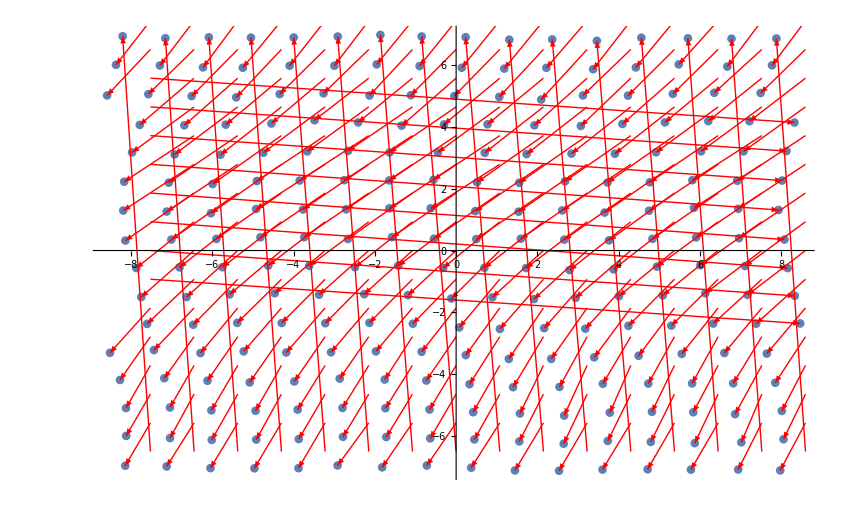

```mathematica
Show[ListPlot[config],Graphics[  {Red,Arrowheads[0.01],Map[Arrow,Thread[{reference,reference+((config-reference))}]] }  ,Axes->True,AspectRatio->0.5,ImageSize->800,PlotRange->{{-9,9},{-9,9}}]]
```